# Golden Ratio Spiral

## A first aproach:

In this first aproach to the probleml a function was created, this function recieves as input the size of the square and automatically generates 9 subsections of the spiral, reducing each time its size as given by the golden ratio.
The 9 subsections of the spiral are contained inside the funtion and were manually written.
Two parametric plots are used: The first one creates the squares while the second one creates the spiral sections

```mathematica
spiralSqV1[rr_]:=Module[{α,sq,sp,t},α=N[1/GoldenRatio];
	sq=ParametricPlot[{{t,rr},{rr,t},
		{α*t+rr,rr},{rr+α*rr,t},
		{α*t+rr,rr*α},{rr+α^3*rr,s},
		{α^3*t+rr,rr-α^3*rr},{rr+α^4*rr,α^2rr+α^2*s},
		{α^5t+rr+α^4rr,α*rr+α^5rr},{rr+α^4rr+α^7rr,α*rr+α^4s},
		{α^7t+rr+α^4*rr,rr-α^3rr-α^7rr}},
		{t,0,rr},{s,rr-α^2*rr,rr},PlotRange->{{0,rr+α*rr+α^4rr},{0,rr+α*rr+α^4rr}}];
	sp=ParametricPlot[{rr{Cos[a]+1,-Sin[a]+1},
		α(rr){-Cos[a]+1/α,-Sin[a]+1},
		{-α^2(rr)Cos[a]+rr+α^3(rr),α^2(rr)Sin[a]+α(rr)},
		{α^3(rr)Cos[a]+rr+α^3(rr),α^3(rr)Sin[a]+α(rr)+α^4(rr)},
		{α^4(rr)Cos[a]+rr+α^4(rr),-α^4(rr)Sin[a]+α(rr)+α^4(rr)},
		{-α^5(rr)Cos[a]+rr+α^4(rr),-α^5(rr)Sin[a]+α(rr)+α^5(rr)},
		{-α^6(rr)Cos[a]+rr+α^4(rr)+α^7(rr),α^6(rr)Sin[a]+α(rr)+α^5(rr)},
		{α^7(rr)Cos[a]+rr+α^4(rr)+α^7(rr),α^7(rr)Sin[a]+α(rr)+α^5(rr)+α^8(rr)},
		{α^8(rr)Cos[a]+rr+α^4(rr)+α^8(rr),-α^8(rr)Sin[a]+α(rr)+α^5(rr)+α^8(rr)}},
		{a,Pi/2,Pi}];
		Return[Show[sq,sp,ImageSize->Large]]
	]
```

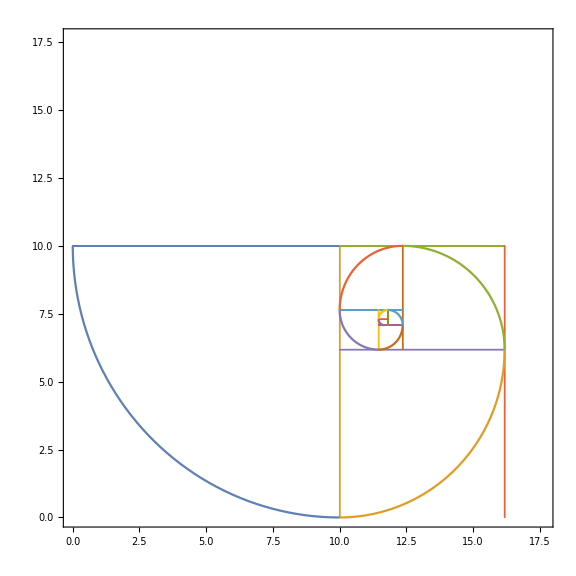

```mathematica
spiralSqV1[10]
```

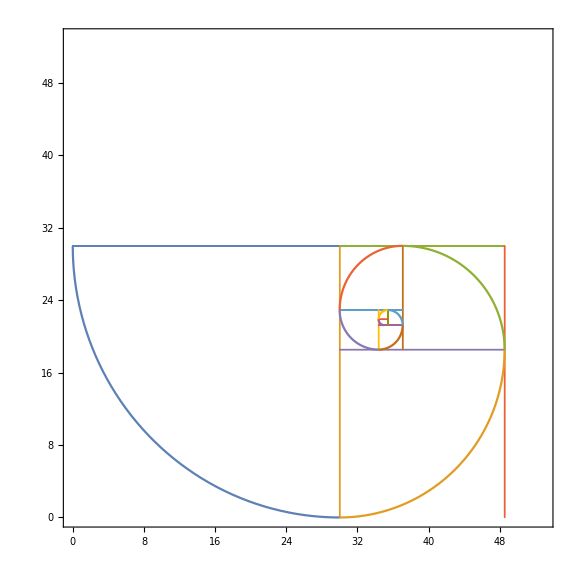

```mathematica
spiralSqV1[30]
```

Later, in a second iteration of the function minor aesthetic changes were made, specifically the plot range changed.

```mathematica
spiralSqV2[rr_]:=Module[{α,sq,sp,t},α=N[1/GoldenRatio];
	sq=ParametricPlot[{
		{t+0,rr},{t+0,0},{rr,t},{0,t},
		{α*t+(rr),α*rr},{α*t+(rr),0},{rr+α*rr,α*t},{rr,α*t},
		{α^2*t+rr+α^3*rr,rr},{α^2*t+rr+α^3*rr,α*rr},{rr+α*rr,α^2*t+α*rr},{rr+α^3*rr,α^2*t+α*rr},
		{α^3*t+rr,α*rr+α^2*rr},{α^3*t+rr,α*rr+α^4*rr},{rr+α^3*rr,α^3*t+α*rr+α^4*rr},{rr,α^3*t+α*rr+α^4*rr},
		{α^4t+rr,α*rr+α^4rr},{α^4t+rr,α*rr},{rr+α^4rr,α^4*t+α*rr},{rr,α^4*t+α*rr},
		{α^5t+rr+α^4*rr,α*rr+α^5*rr},{α^5t+rr+α^4*rr,α*rr},{rr+α^3*rr,α^5*t+α*rr},{rr+α^4*rr,α^5*t+α*rr}},
		{t,0,rr},
		PlotRange->{{0,rr+α*rr+α^4rr},{0,rr+α^4rr}}];
	sp=ParametricPlot[{{rr*Cos[a]+rr,-rr*Sin[a]+α^2(rr)+α^3(rr)+α^3(rr)+α^4(rr)},
		{-α(rr)Cos[a]+(rr),-α(rr)Sin[a]+α^3(rr)+α^4(rr)+α^4(rr)+α^5(rr)},
		{-α^2(rr)Cos[a]+rr+α^3(rr),α^2(rr)Sin[a]+α^3(rr)+α^4(rr)+α^4(rr)+α^5(rr)},
		{α^3(rr)Cos[a]+rr+α^3(rr),α^3(rr)Sin[a]+α^2(rr)+α^3(rr)+α^4(rr)},
		{α^4(rr)Cos[a]+rr+α^4(rr),-α^4(rr)Sin[a]+α^2(rr)+α^3(rr)+α^4(rr)},
		{-α^5(rr)Cos[a]+rr+α^4(rr),-α^5(rr)Sin[a]+α^2(rr)+α^3(rr)+α^5(rr)},
		{-α^6(rr)Cos[a]+rr+α^4(rr)+α^7(rr),α^6(rr)Sin[a]+α^2(rr)+α^3(rr)+α^5(rr)},
		{α^7(rr)Cos[a]+rr+α^4(rr)+α^7(rr),α^7(rr)Sin[a]+α^2(rr)+α^3(rr)+α^5(rr)+α^8(rr)},
		{α^8(rr)Cos[a]+rr+α^4(rr)+α^8(rr),-α^8(rr)Sin[a]+α^2(rr)+α^3(rr)+α^5(rr)+α^8(rr)}},
		{a,Pi/2,Pi}];
		Return[Show[sq,sp,ImageSize->Large]]
	]
```

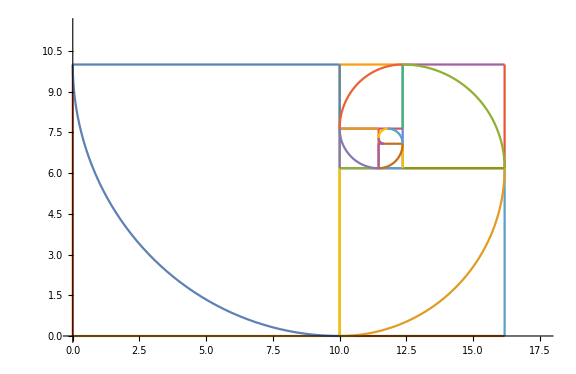

```mathematica
spiralSqV2[10]
```

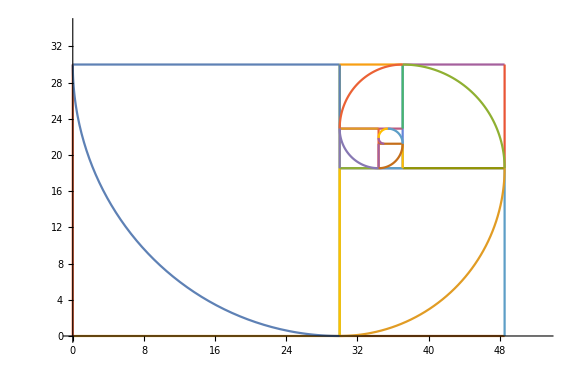

```mathematica
spiralSqV2[30]
```

## For n number of spiral sections

The logical second step was to automatically generate a given number of spiral section, this is possible because all the sections have the same shape, we just have to take into account 2 important things:
	1. The first and easiest to understand is that even if the size of the sections change they do it with a given ratio, the golden ratio.
	2. The second one is that the centers of the circles will “rotate”, more specifically, the centers of the circle move along the inner 		lines of the squares, but we can find a pattern for the movement and we can add it to a general expression that finds the location of 		the centers for any iteration.
**This time only the spiral is generated, maybe in a later iteration the squares will be added.
Also, each section of the spiral doesn’t have a solid color, like in the past versions, this time a continous pallete was given for all the sections so the blend together and it has a better aesthetic.
The axis were conserved to see the effect of the golden ratio recution in size.

```mathematica
SpiralV1[n_,r_]:=Module[{α,a1,a2,b,c,i,j,y,x,p},
	α=N[1/GoldenRatio];
	c=Table[a1=Cos[j*Pi/4]/Abs[Cos[j*Pi/4]];
		a2=-Sin[j*Pi/4]/Abs[Sin[j*Pi/4]];
		{a1*Cos[b],a2*Sin[b]},{j,1,n*2,2}];
	y=r;
	x=r;
	For[i=0,i<n,i++,c⟦i+1⟧=c⟦i+1⟧*α^i(r)];
	c⟦1,1⟧=c⟦1,1⟧+x;
	c⟦1,2⟧=c⟦1,2⟧+y;
	p=1;
	For[i=2,i≤n,i++,
		If[Mod[i,2]==0,
			If[Mod[p,2]>0,y=y-α^i(r),y=y+α^i(r)],
			If[Mod[p,2]==0,x=x-α^i(r),x=x+α^i(r)];
			p++];
		c⟦i,1⟧=c⟦i,1⟧+x;
		c⟦i,2⟧=c⟦i,2⟧+y;
	];
	ParametricPlot[c,{b,Pi/2,Pi},PlotRange->{{0,r+α*r+α^4r},{0,r+α^4r}},ColorFunction->"DarkRainbow",ImageSize->Full,PlotStyle->Thin]]
```

α:  Contains the value for the golden ratio.
c:  Is a table with as many entrys as sections of the golden spiral you wish.
a1 and a2: Have values of 1 or -1, depending of the value of the Cosine and Sine respectively used for each spiral section. When mulplying any combination of this two values, with Cosine and Sine, the quarter of circle that is plotted changes. **Maybe adding Pi/4 or something like that the rotation of the whole spiral can change.
x and y give the positions of the centers of the circles.
p is a counter used to know if the center moves up, down, left and right.

#### Same size, different number of sections.

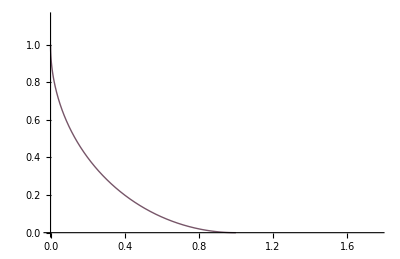

```mathematica
SpiralV1[1,1]
```

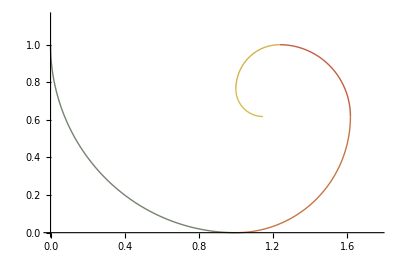

```mathematica
SpiralV1[5,1]
```

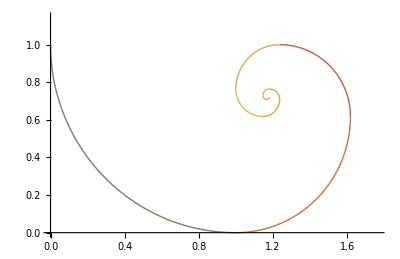

```mathematica
SpiralV1[10,1]
```

#### Different size, same number of sections.

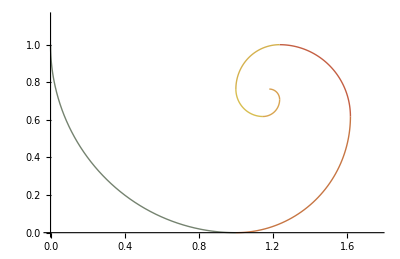

```mathematica
SpiralV1[7,1]
```

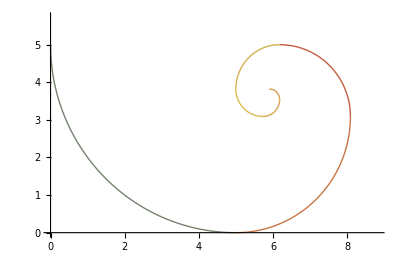

```mathematica
SpiralV1[7,5]
```

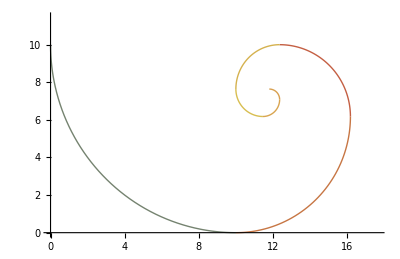

```mathematica
SpiralV1[7,10]
```

## Adding manipulate

The parametric plot that creates the spiral was used inside the Manipulate function to see the spiral develope.

```mathematica
SpiralV2[n_,r_]:=Module[{α,a1,a2,b,c,i,j,y,x,p},
	α=N[1/GoldenRatio];
	c=Table[a1=Cos[j*Pi/4]/Abs[Cos[j*Pi/4]];
		a2=-Sin[j*Pi/4]/Abs[Sin[j*Pi/4]];
		{a1*Cos[b],a2*Sin[b]},{j,1,n*2,2}];
	y=r;
	x=r;
	For[i=0,i<n,i++,c⟦i+1⟧=c⟦i+1⟧*α^i(r)];
	c⟦1,1⟧=c⟦1,1⟧+x;
	c⟦1,2⟧=c⟦1,2⟧+y;
	p=1;
	For[i=2,i≤n,i++,
		If[Mod[i,2]==0,
			If[Mod[p,2]>0,y=y-α^i(r),y=y+α^i(r)],
			If[Mod[p,2]==0,x=x-α^i(r),x=x+α^i(r)];
			p++];
		c⟦i,1⟧=c⟦i,1⟧+x;
		c⟦i,2⟧=c⟦i,2⟧+y;
	];
	Manipulate[ParametricPlot[c,{b,Pi/2,e},PlotRange->{{0,r+α*r+α^4r},{0,r+α^4r}},ColorFunction->"DarkRainbow",ImageSize->Full,PlotStyle->Thin],{e,Pi/2+0.001(Pi/2),Pi}]]
```

```mathematica
SpiralV2[13,1]
```

e is the parameter that increases whe the slider moves right.
An important thing to note is the fact that even if the centers of the circles are correctly placed, the circles start drawing from an incorrect direction.

## Correcting circle formation

Its worth mentioning that only the unpair sections startcounterclockwise which should be corrected.

```mathematica
SpiralV3[n_,r_]:=Module[{α,a1,a2,b,c,i,j,y,x,p},
	α=N[1/GoldenRatio];
	c=Table[a1=Cos[j*Pi/4]/Abs[Cos[j*Pi/4]];
		a2=-Sin[j*Pi/4]/Abs[Sin[j*Pi/4]];
		{a1*Cos[b],a2*Sin[b]},{j,1,n*2,2}];
	y=r;
	x=r;
	For[i=0,i<n,i++,c⟦i+1⟧=c⟦i+1⟧*α^i(r)];
	c⟦1,1⟧=c⟦1,1⟧+x;
	c⟦1,2⟧=c⟦1,2⟧+y;
	p=1;
	For[i=2,i≤n,i++,
		If[Mod[i,2]==0,
			If[Mod[p,2]>0,y=y-α^i(r),y=y+α^i(r)],
			If[Mod[p,2]==0,x=x-α^i(r),x=x+α^i(r)];
			p++];
		c⟦i,1⟧=c⟦i,1⟧+x;
		c⟦i,2⟧=c⟦i,2⟧+y;
	];
	Manipulate[ParametricPlot[c,{b,Pi/2,e},PlotRange->{{0,r+α*r+α^4r},{0,r+α^4r}},ColorFunction->"DarkRainbow",ImageSize->Full,PlotStyle->Thin],{e,Pi/2+0.001(Pi/2),Pi}]]
```

```mathematica
SpiralV3[13,1]
```

```mathematica
Manipulate[ParametricPlot[{Cos[b],Sin[b]},{b,Pi/2,e},PlotRange->{{-1,1},{0,1}}],{e,Pi/2+0.0001Pi,Pi}]
```